```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 391 Kb

{Utilities`CleanSlate`,Parallel`Debug`Perfmon`,Parallel`Debug`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,System`,Global`}

```mathematica
Clear[𝒱]
𝒱 = V0 ( Exp[ - α ] + Exp[ - β ] + Exp[ - γ ] )
```

(ⅇ^-α+ⅇ^-β+ⅇ^-γ) V0

```mathematica
Clear[αβγReplace]
αβγReplace = {
α -> (2 π)/3+ θ2[t] - θ1[t] ,
β -> (2 π)/3+ θ3[t] - θ2[t] ,
γ-> (2 π)/3+ θ1[t] - θ3[t]
};
αβγReplace // TableForm
```

α→(2 π)/3-θ1[t]+θ2[t]
β→(2 π)/3-θ2[t]+θ3[t]
γ→(2 π)/3+θ1[t]-θ3[t]

```mathematica
Clear[V]
V = 
𝒱 /. αβγReplace // FullSimplify
```

ⅇ^(-2 π/3) (ⅇ^(θ1[t]-θ2[t])+ⅇ^(θ2[t]-θ3[t])+ⅇ^(-θ1[t]+θ3[t])) V0

```mathematica
Clear[q]
q = { θ1[t] , θ2[t] , θ3[t] }
```

{θ1[t],θ2[t],θ3[t]}

```mathematica
D[q, t]
```

{θ1'[t],θ2'[t],θ3'[t]}

```mathematica
D[q, t] . D[q, t]
```

θ1'[t]^2+θ2'[t]^2+θ3'[t]^2

```mathematica
Clear[T] 
T = 1/2 B ( D[q, t] . D[q, t] )
```

1/2 B (θ1'[t]^2+θ2'[t]^2+θ3'[t]^2)

```mathematica
Clear[ℒ]
ℒ = T - V
```

-ⅇ^(-2 π/3) (ⅇ^(θ1[t]-θ2[t])+ⅇ^(θ2[t]-θ3[t])+ⅇ^(-θ1[t]+θ3[t])) V0+1/2 B (θ1'[t]^2+θ2'[t]^2+θ3'[t]^2)

```mathematica
D[ D[ ℒ , D[q[[1]], t] ], t ] - D[ ℒ , q[[1]] ]  
D[ D[ ℒ , D[q[[2]], t] ], t ] - D[ ℒ , q[[2]] ]  
D[ D[ ℒ , D[q[[3]], t] ], t ] - D[ ℒ , q[[3]] ]
```

ⅇ^(-2 π/3) (ⅇ^(θ1[t]-θ2[t])-ⅇ^(-θ1[t]+θ3[t])) V0+B θ1''[t]

ⅇ^(-2 π/3) (-ⅇ^(θ1[t]-θ2[t])+ⅇ^(θ2[t]-θ3[t])) V0+B θ2''[t]

ⅇ^(-2 π/3) (-ⅇ^(θ2[t]-θ3[t])+ⅇ^(-θ1[t]+θ3[t])) V0+B θ3''[t]

```mathematica
Table[
D[ D[ ℒ , D[q[[i]], t] ], t ] - D[ ℒ , q[[i]] ] , 
{ i, 1, 3 } ] // TableForm
```

ⅇ^(-2 π/3) (ⅇ^(θ1[t]-θ2[t])-ⅇ^(-θ1[t]+θ3[t])) V0+B θ1''[t]
ⅇ^(-2 π/3) (-ⅇ^(θ1[t]-θ2[t])+ⅇ^(θ2[t]-θ3[t])) V0+B θ2''[t]
ⅇ^(-2 π/3) (-ⅇ^(θ2[t]-θ3[t])+ⅇ^(-θ1[t]+θ3[t])) V0+B θ3''[t]

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q, t ] ;
eqs // TableForm
```

-ⅇ^(-2 π/3) (ⅇ^(θ1[t]-θ2[t])-ⅇ^(-θ1[t]+θ3[t])) V0-B θ1''[t]==0
-ⅇ^(-2 π/3) (-ⅇ^(θ1[t]-θ2[t])+ⅇ^(θ2[t]-θ3[t])) V0-B θ2''[t]==0
-ⅇ^(-2 π/3) (-ⅇ^(θ2[t]-θ3[t])+ⅇ^(-θ1[t]+θ3[t])) V0-B θ3''[t]==0

```mathematica
Clear[parameters]
parameters = { 
V0 -> 1 , 
B -> 1 
} ;
parameters // TableForm
```

V0→1
B→1

```mathematica
eqs /. parameters  // TableForm
```

-ⅇ^(-2 π/3) (ⅇ^(θ1[t]-θ2[t])-ⅇ^(-θ1[t]+θ3[t]))-θ1''[t]==0
-ⅇ^(-2 π/3) (-ⅇ^(θ1[t]-θ2[t])+ⅇ^(θ2[t]-θ3[t]))-θ2''[t]==0
-ⅇ^(-2 π/3) (-ⅇ^(θ2[t]-θ3[t])+ⅇ^(-θ1[t]+θ3[t]))-θ3''[t]==0

```mathematica
Clear[ics]
ics = {
θ1[0] == 0.1 , 
θ1'[0] == 0 , 
θ2[0] ==  - 0.05 , 
θ2'[0] == 0 , 
θ3[0] == 0.15 , 
θ3'[0] == 0 
} ;
ics // TableForm
```

θ1[0]==0.1
θ1'[0]==0
θ2[0]==-0.05
θ2'[0]==0
θ3[0]==0.15
θ3'[0]==0

```mathematica
Clear[solution]
solution[t_] = 
First[ NDSolve[ Union[ eqs /. parameters , ics ] , q , { t, 0, 300 } ] ]
```

{θ1[t]→InterpolatingFunction[…][t],θ2[t]→InterpolatingFunction[…][t],θ3[t]→InterpolatingFunction[…][t]}

```mathematica
Plot[ Evaluate[ q /. solution[t] ]  , { t, 0, 20 } , PlotLabels-> q  ]
```

-Graphics-

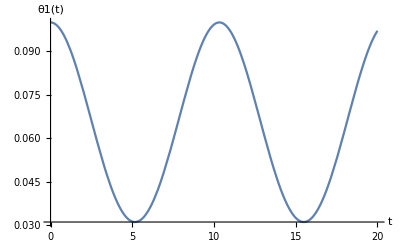

```mathematica
Plot[ q[[1]] /. solution[t] , { t, 0, 20 }, AxesLabel-> { t , q[[1]] }  ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]  ,
{ tmax , 0.01 , 30 } ]
```

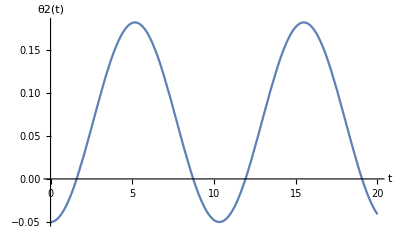

```mathematica
Plot[ q[[2]] /. solution[t] , { t, 0, 20 }, AxesLabel-> { t , q[[2]] }  ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[2,2]] , solution'[t][[2,2]] } , { t , 0, tmax } , AxesLabel-> { q[[2]] , D[q[[2]], t] } ]  ,
{ tmax , 0.01 , 30  } ]
```

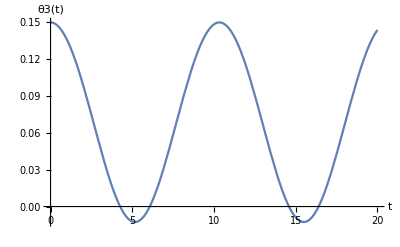

```mathematica
Plot[ q[[3]] /. solution[t] , { t, 0, 20 }, AxesLabel-> { t , q[[3]] }  ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[3,2]] , solution'[t][[3,2]] } , { t , 0, tmax } , AxesLabel-> { q[[3]] , D[q[[3]], t] } ]  ,
{ tmax , 0.01 , 30  } ]
```